Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

March 2, 2021

To: Chief Scientist, Vertextin Inc.
From: Aakriti Lakshmanan
Subj: Analysis of CNS Drug Effectiveness

## Summary and Introduction

### Abstract:

As requested in the Scope of Work of February 16, 2011, we evaluated 36 drugs in a comprehensive dataset for a wide variety of parameters. Specifically, we wanted to evaluate these 36 drugs for their effectiveness as central nervous system (CNS) drugs by evaluating their ability to cross the blood-brain barrier (BBB).

## Methodology

For this study, the list of 36 drugs was collected from the NCSSM Canvas website. The following analyses were conducted:

Drug data was imported into Mathematica

Data was summarized through descriptive statistics

Data was filtered by MW and TPSA to find viable drugs for CNS applications.

The Abraham solvation parameter equation was used to predict the logBB of each drug.

### Data Import and Description:

```mathematica
smallDrugDataset = Import["/Users/aakritilakshmanan/Downloads/completedrugdata.csv"];
viableDrug=smallDrugDataset;
smallDrugDataset // TableForm
```

Name | MW | TPSA | Rings | Donors | Acceptors | Rotatable | logP | Vd | Sw | logSw | A | B | Bo | L | S | E | V | pKaAcid | pKaBase | Ionizable
Adefovir | 273.19 | 146.19 | 2 | 4 | 9 | 5 | -1.94 | 0.32 | 3.93 | 0.59439 | 0.85 | 2.28 | 2.31 | 11.341 | 2.46 | 2.34 | 1.785 | 1.9 | 3.9 | 2
Advil | 206.28 | 37.3 | 1 | 1 | 2 | 4 | 3.44 | 0.17 | 0.00566 | -2.24718 | 0.57 | 0.51 | 0.53 | 7.248 | 1.01 | 0.78 | 1.7771 | 4.3 |  | 1
Akineton | 311.46 | 23.47 | 4 | 1 | 2 | 5 | 4.19 | 8.04 | 0.0716 | -1.14509 | 0.31 | 1.17 | 1.19 | 11.784 | 1.32 | 1.75 | 2.6196 |  | 10.3 | 1
Albuterol | 239.31 | 72.72 | 1 | 4 | 4 | 5 | 0.23 | 2.07 | 9.89 | 0.9952 | 1.19 | 1.82 | 1.82 | 9.21 | 1.26 | 1.43 | 1.9786 | 10.3 | 8.6 | 2
Allegra | 501.65 | 81 | 4 | 3 | 5 | 10 | 4.35 | 1.63 | 0.0118 | -1.92812 | 1.2 | 2.12 | 2.14 | 18.782 | 2.48 | 2.72 | 4.0876 | 4.3 | 8.6 | 2
Amoxicillin | 365.4 | 158.26 | 3 | 5 | 8 | 4 | -1.08 | 0.26 | 2.97 | 0.47276 | 1.55 | 2.9 | 2.9 | 16.505 | 3.22 | 2.7 | 2.5356 | 2.6 | 7.3 | 3
Aripiprazole | 448.38 | 44.81 | 4 | 1 | 5 | 7 | 4.38 | 4.64 | 0.012 | -1.92082 | 0.41 | 1.75 | 1.77 | 17.506 | 2.53 | 2.63 | 3.2755 |  | 7.6 | 2
Aspirin | 180.16 | 63.6 | 1 | 1 | 4 | 3 | 1.22 | 0.23 | 3.07 | 0.48714 | 0.57 | 0.57 | 0.78 | 6.113 | 1.42 | 0.84 | 1.2879 | 3.5 |  | 1
Balofloxacin | 389.42 | 82.11 | 4 | 2 | 7 | 5 | -0.28 | 1.97 | 0.00812 | -2.09044 | 0.72 | 2.03 | 2.05 | 14.509 | 2.58 | 2.23 | 2.786 | 6.1 | 9.3 | 4
Biapenem | 353.42 | 124.84 | 4 | 2 | 8 | 4 | 2.7 | 0.22 | 1.05 | 0.02119 | 0.88 | 2.05 | 2.04 | 14.095 | 2.22 | 2.15 | 2.4347 | 2.9 |  | 1
Celebrex | 381.37 | 85.84 | 3 | 2 | 5 | 4 | 2.9 | 2.05 | 0.00412 | -2.3851 | 0.44 | 1.22 | 1.24 | 12.59 | 2.43 | 2.51 | 2.4672 | 9.7 | 1.6 | 2
Diabinese | 276.74 | 83.65 | 1 | 2 | 5 | 4 | 2.33 | 0.18 | 0.293 | -0.53313 | 0.59 | 1.13 | 1.12 | 10.542 | 2.38 | 1.46 | 1.8986 | 4.6 |  | 1
Dutasteride | 528.53 | 58.2 | 5 | 2 | 4 | 4 | 5.33 | 3.78 | 0.0056 | -2.25181 | 0.73 | 1.4 | 1.45 | 16.137 | 3.2 | 1.69 | 3.5345 |  |  | 0
Ertapenem | 475.51 | 181.57 | 4 | 5 | 10 | 7 | 1.49 | 0.28 | 2.56 | 0.40824 | 2 | 3.23 | 3.26 | 20.64 | 3.55 | 3.2 | 3.3038 | 3.2 | 7.9 | 3
Ezetimibe | 409.42 | 60.77 | 4 | 2 | 4 | 6 | 3.64 | 2.12 | 0.0169 | -1.77211 | 0.81 | 1.77 | 1.81 | 15.908 | 2.61 | 2.65 | 2.9369 | 10.3 |  | 1
Flonase | 500.57 | 105.97 | 4 | 1 | 5 | 6 | 2.66 | 1.94 | 0.00604 | -2.21896 | 0.39 | 1.84 | 1.87 | 15.558 | 3.27 | 2 | 3.4915 |  |  | 0
Floxetine | 309.33 | 21.26 | 2 | 1 | 2 | 7 | 4.84 | 9.78 | 0.0611 | -1.21396 | 0.13 | 0.78 | 0.81 | 8.916 | 1.19 | 1.01 | 2.24 |  | 9.9 | 1
Frovatriptan | 243.3 | 70.91 | 3 | 4 | 4 | 2 | 0.97 | 1.93 | 0.295 | -0.53018 | 0.93 | 1.33 | 1.3 | 11.294 | 2.1 | 2.08 | 1.8985 |  | 8.8 | 1
Gefitinib | 446.9 | 68.74 | 4 | 1 | 7 | 8 | 4.76 | 6.71 | 0.00131 | -2.88273 | 0.25 | 1.87 | 1.86 | 16.271 | 2.97 | 2.76 | 3.1453 |  | 7.4 | 3
Hydrochorathiazide | 297.74 | 135.12 | 2 | 4 | 7 | 1 | -0.38 | 0.81 | 0.949 | -0.02273 | 1.01 | 1.76 | 1.76 | 10.931 | 2.77 | 2.15 | 1.7323 | 8.9 |  | 2
Ibuprofen | 206.28 | 37.3 | 1 | 1 | 2 | 4 | 3.44 | 0.17 | 0.0566 | -1.24718 | 0.57 | 0.51 | 0.53 | 7.248 | 1.01 | 0.78 | 1.7771 | 4.3 |  | 1
Landiolol | 509.59 | 127.82 | 3 | 3 | 11 | 14 | 0.76 | 1.46 | 0.966 | -0.01502 | 0.47 | 3.02 | 3.01 | 18.761 | 3.02 | 2.04 | 3.8593 |  | 7.9 | 1
Naproxen | 230.26 | 46.53 | 2 | 1 | 3 | 3 | 3.01 | 0.17 | 0.183 | -0.73755 | 0.57 | 0.75 | 0.76 | 8.627 | 1.49 | 1.54 | 1.7821 | 4.3 |  | 1
Nexium | 345.42 | 92.35 | 3 | 0 | 6 | 5 | 1.61 | 2.21 | 0.5 | -0.30103 | 0 | 1.96 | 1.79 | 12.538 | 2.18 | 2.35 | 2.5161 |  | 7.8 | 2
Nitisone | 329.23 | 100.04 | 2 | 0 | 6 | 4 | 3.25 | 0.26 | 0.0984 | -1.007 | 0 | 1.03 | 1.04 | 9.985 | 2.55 | 1.36 | 2.0091 | 3.1 |  | 1
Nitroglycerine | 227.09 | 174.18 | 0 | 0 | 12 | 8 | 1.69 | 1.42 | 0.153 | -0.81531 | 0 | 0.45 | 0.32 | 6.225 | 1.87 | 0.58 | 1.23 |  |  | 0
Norvasc | 408.87 | 99.88 | 2 | 3 | 7 | 10 | 0.65 | 4.1 | 0.148 | -0.82974 | 0.36 | 2.19 | 2.19 | 13.28 | 2.26 | 1.65 | 3.0239 |  | 9.6 | 2
Oxycodone | 315.36 | 59 | 4 | 1 | 5 | 1 | -0.28 | 2.15 | 3.57 | 0.55267 | 0.23 | 1.8 | 1.79 | 12.246 | 2.28 | 2.18 | 2.2644 |  | 8.3 | 1
Plavix | 321.82 | 57.78 | 3 | 0 | 3 | 4 | 3.12 | 2.33 | 0.0977 | -1.01011 | 0 | 0.98 | 0.99 | 10.652 | 1.71 | 1.72 | 2.2823 |  | 1.2 | 1
Prednisone | 358.43 | 91.67 | 4 | 2 | 5 | 2 | 1.4 | 1.27 | 0.113 | -0.94692 | 0.41 | 1.97 | 1.96 | 13.248 | 3.25 | 2.19 | 2.7116 |  |  | 0
Toprol | 267.36 | 50.72 | 1 | 2 | 4 | 9 | 1.72 | 3.16 | 2.41 | 0.38202 | 0.29 | 1.52 | 1.51 | 9.58 | 1.22 | 1.1 | 2.2604 |  | 9.6 | 1
Valium | 284.74 | 32.67 | 3 | 0 | 3 | 1 | 2.84 | 1.93 | 0.0701 | -1.15428 | 0 | 1.04 | 1.04 | 11.132 | 1.72 | 2.11 | 2.0739 |  | 3.2 | 1
Wellbutrin | 239.74 | 29.1 | 1 | 1 | 2 | 4 | 3.37 | 3.42 | 0.139 | -0.85699 | 0.13 | 0.94 | 0.94 | 8.037 | 1.32 | 1.07 | 1.9406 |  | 7.6 | 1
Zocor | 418.56 | 72.83 | 3 | 1 | 5 | 7 | 4.87 | 2.27 | 0.00301 | -2.52143 | 0.31 | 1.45 | 1.49 | 14.478 | 2.29 | 1.35 | 3.4268 |  |  | 0
Zoloft | 306.23 | 12.03 | 3 | 1 | 1 | 2 | 4.9 | 9.6 | 0.0146 | -1.83565 | 0.13 | 0.67 | 0.68 | 10.748 | 1.44 | 1.83 | 2.2647 |  | 9.5 | 1
Zyrtec | 388.89 | 53.01 | 3 | 1 | 5 | 8 | 2.95 | 0.34 | 0.356 | -0.44855 | 0.57 | 1.76 | 1.78 | 13.639 | 2.24 | 2.05 | 2.9388 | 3.8 | 7.9 | 3

## Results

### Descriptive Statistics

We determined the mean, median, standard deviation, and quartiles for our data set, and produced a box/whisker plot for each of the three variables. As can be seen in the box/whisker plot of each parameter, each of the parameters have values that mostly range between a two specific quartile values. Molecular weight has the highest standard deviation, which is good for this dataset as molecular weight is one of the parameters for the Abraham solvation parameter equation, and variance in this parameter will allow us to examine different logBB values. Most of the molecules examined have between 2 to 4 rings, 1 to 2.5 hydrogen donors, an 3.5 to 7 hydrogen acceptors.

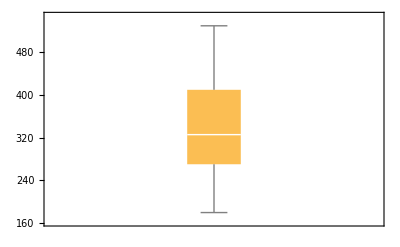
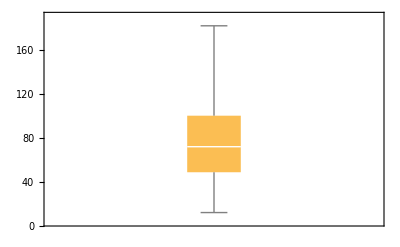
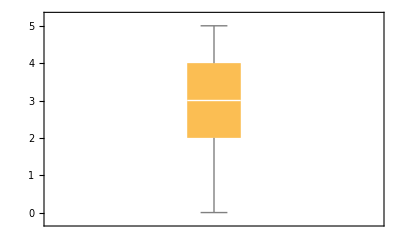
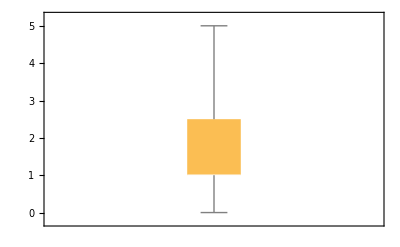
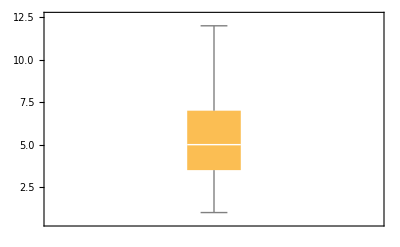
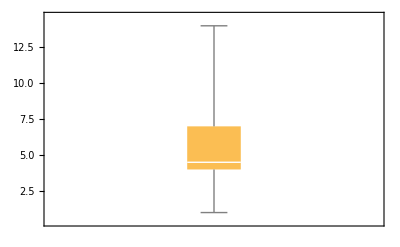
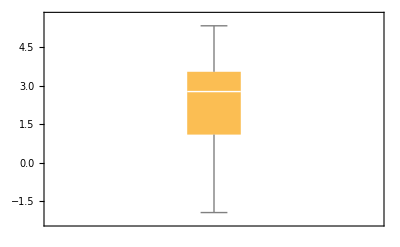
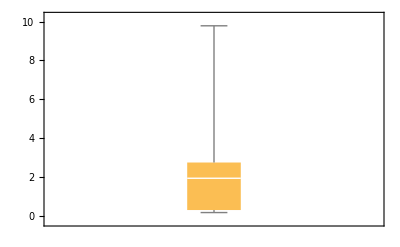
| MW | TPSA | Rings | Donors | Acceptors | Rotatable | logP | Vd | logSw
Mean | 341.554 | 78.9789 | 49/18 | 65/36 | 187/36 | 187/36 | 2.3625 | 2.37194 | -0.915431
Median | 325.525 | 71.815 | 3 | 1 | 5 | 9/2 | 2.77 | 1.935 | -0.901955
Standard Deviation | 95.5158 | 43.0459 | (√(71/5))/3 | (√(2507/35))/6 | (√(8627/35))/6 | (√(10211/35))/6 | 1.85822 | 2.54746 | 1.04246
Quartiles | {270.275,325.525,409.145} | {48.625,71.815,99.96} | {2,3,4} | {1,1,5/2} | {7/2,5,7} | {4,9/2,7} | {1.095,2.77,3.54} | {0.3,1.935,2.745} | {-1.87824,-0.901955,-0.018875}
BoxWhisker Plot | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
header = smallDrugDataset[[1]];
smallDrugDataset = Delete[smallDrugDataset,1];
{name, mw, tpsa,rings,donors,acceptors,rotatable,logP,vd,sw,logSw,a,b,bo,l,s,e,v,pKaAcid,pKaBase,ionizable}= Transpose[smallDrugDataset];
descriptiveStats = Grid[{{"", "MW", "TPSA", "Rings", "Donors", "Acceptors", "Rotatable", "logP", "Vd", "logSw"}, {"Mean", Mean[mw], Mean[tpsa], Mean[rings], Mean[donors], Mean[acceptors], Mean[rotatable], Mean[logP], Mean[vd], Mean[logSw]}, {"Median", Median[mw], Median[tpsa], Median[rings], Median[donors], Median[acceptors], Median[rotatable], Median[logP], Median[vd], Median[logSw]}, {"Standard Deviation", StandardDeviation[mw], StandardDeviation[tpsa], StandardDeviation[rings], StandardDeviation[donors], StandardDeviation[acceptors], StandardDeviation[rotatable], StandardDeviation[logP], StandardDeviation[vd], StandardDeviation[logSw]}, {"Quartiles", Quartiles[mw], Quartiles[tpsa], Quartiles[rings], Quartiles[donors], Quartiles[acceptors], Quartiles[rotatable], Quartiles[logP], Quartiles[vd], Quartiles[logSw]}, {"BoxWhisker Plot", BoxWhiskerChart[mw], BoxWhiskerChart[tpsa], BoxWhiskerChart[rings], BoxWhiskerChart[donors], BoxWhiskerChart[acceptors], BoxWhiskerChart[rotatable], BoxWhiskerChart[logP], BoxWhiskerChart[vd], BoxWhiskerChart[logSw]}}, Frame -> All]
```

### van de Waterbeemd Method

H.van de Waterbeemd and colleagues determined that any drug that has a topological polar surface area (TPSA) of 90 A2 (square angstroms) or greater and a molecular weight of 450 grams/mol is not able to penetrate the BBB and enter into the central nervous system. Based on this rule, we evaluated our dataset and determined that there are 23 compounds out of 36 that are capable of crossing the BBB. They are listed below:

```mathematica
Grid[
Map[
{
#[[1]],
#[[2]],
#[[3]],
#[[4]],
#[[5]],
#[[6]],
#[[7]],
#[[8]]
} &,
DeleteCases[viableDrug, a_ /; Or[a[[3]] >90, a[[2]]>450]]
],
Frame -> All]
```

Name | MW | TPSA | Rings | Donors | Acceptors | Rotatable | logP
Advil | 206.28 | 37.3 | 1 | 1 | 2 | 4 | 3.44
Akineton | 311.46 | 23.47 | 4 | 1 | 2 | 5 | 4.19
Albuterol | 239.31 | 72.72 | 1 | 4 | 4 | 5 | 0.23
Aripiprazole | 448.38 | 44.81 | 4 | 1 | 5 | 7 | 4.38
Aspirin | 180.16 | 63.6 | 1 | 1 | 4 | 3 | 1.22
Balofloxacin | 389.42 | 82.11 | 4 | 2 | 7 | 5 | -0.28
Celebrex | 381.37 | 85.84 | 3 | 2 | 5 | 4 | 2.9
Diabinese | 276.74 | 83.65 | 1 | 2 | 5 | 4 | 2.33
Ezetimibe | 409.42 | 60.77 | 4 | 2 | 4 | 6 | 3.64
Floxetine | 309.33 | 21.26 | 2 | 1 | 2 | 7 | 4.84
Frovatriptan | 243.3 | 70.91 | 3 | 4 | 4 | 2 | 0.97
Gefitinib | 446.9 | 68.74 | 4 | 1 | 7 | 8 | 4.76
Ibuprofen | 206.28 | 37.3 | 1 | 1 | 2 | 4 | 3.44
Naproxen | 230.26 | 46.53 | 2 | 1 | 3 | 3 | 3.01
Oxycodone | 315.36 | 59 | 4 | 1 | 5 | 1 | -0.28
Plavix | 321.82 | 57.78 | 3 | 0 | 3 | 4 | 3.12
Toprol | 267.36 | 50.72 | 1 | 2 | 4 | 9 | 1.72
Valium | 284.74 | 32.67 | 3 | 0 | 3 | 1 | 2.84
Wellbutrin | 239.74 | 29.1 | 1 | 1 | 2 | 4 | 3.37
Zocor | 418.56 | 72.83 | 3 | 1 | 5 | 7 | 4.87
Zoloft | 306.23 | 12.03 | 3 | 1 | 1 | 2 | 4.9
Zyrtec | 388.89 | 53.01 | 3 | 1 | 5 | 8 | 2.95

#### Calculated Method

As described in Chapter 4 (Gotwals, Introduction to Medicinal Chemistry), Stanley Abraham developed an equation to predict the logBB value, a measure of how well a drug crosses the blood - brain barrier. Using the dataset, we created separate variables needed for the equation : A, B, Es, S, and V. Using the Abraham solvation parameter equation found in Chapter 4, we generated a list of predicted logBB values, shown in the table below with the compound name :

```mathematica
mylogbbFunction[e1_,s1_,a1_,b1_,v1_]= 0.044 + 0.511e1 - 0.886 s1 - 0.724 a1 -0.666 b1 + 0.861 v1;
predictedLogBB = List[];
For[i=1,i<(Length[a]+1),i++,AppendTo[predictedLogBB,mylogbbFunction[e[[i]],s[[i]],a[[i]],b[[i]],v[[i]]]]];
logBBtogether = Transpose[{name,predictedLogBB}];
Grid[logBBtogether , Frame ->All]
```

Adefovir | -1.53682
Advil | 0.325463
Akineton | 1.02055
Albuterol | -0.711735
Allegra | 0.475344
Amoxicillin | -2.29967
Aripiprazole | 0.504216
Aspirin | -0.468298
Balofloxacin | -0.576864
Biapenem | -0.730413
Celebrex | 0.166809
Diabinese | -0.863665
Dutasteride | -0.345326
Ertapenem | -2.22071
Ezetimibe | -0.150899
Flonase | -0.332839
Floxetine | 0.82081
Frovatriptan | -0.678212
Gefitinib | 0.104623
Hydrochorathiazide | -1.72346
Ibuprofen | 0.325463
Landiolol | -0.618023
Naproxen | 0.133008
Nexium | 0.174372
Nitisone | -0.476485
Nitroglycerine | -0.55711
Norvasc | -0.230812
Oxycodone | -0.277772
Plavix | 0.72024
Prednisone | -0.990582
Toprol | 0.249104
Valium | 0.691278
Wellbutrin | 0.371947
Zocor | 0.465245
Zoloft | 1.11286
Zyrtec | 0.0523768

We prepared a box/whisker plot of this data, showing that most of our drugs have a logBB value between - 0.7 and 0.3. Generally, compounds with a logBB above 0 are able to penetrate the BBB, while compounds with a logBB below 0 are unable to penetrate the BBB. Given these restrictions, 17 of the 36 drugs examined would be able to penetrate the BBB.

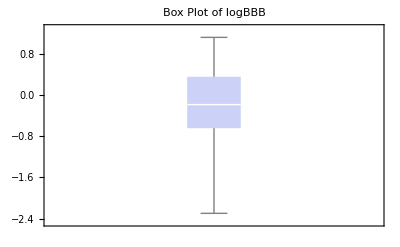

```mathematica
BoxWhiskerChart[predictedLogBB, PlotTheme->"Classic",PlotLabel->HoldForm[Box Plot of logBBB],LabelStyle->{FontFamily->"Times New Roman",14,GrayLevel[0]} ]
```

Genez very much appreciates the opportunity to conduct this work and hopes that the results are satisfactory. We look forward to a long working relationship with Vertextin, and wish your company success in its scientific ventures.

I certify that this work was completed by me on March 2, 2021.  All references and resources are cited.  Assistance was provided by NAME OF PERSON(S) (if any)
  Electronic signature: -Graphics-

References: